```mathematica
L1 = {{-Subscript[k, 0]-π/Subscript[T, 2]-I π J,Subscript[k, 0]},{Subscript[k, 0],-Subscript[k, 0]-π/Subscript[T, 2]+I π J}}
```

{{-ⅈ J π-k_0-π/T_2,k_0},{k_0,ⅈ J π-k_0-π/T_2}}

```mathematica
L2 ={{-3 Subscript[k, 0]-π/Subscript[T, 2]-3I π J,3 Subscript[k, 0],0,0},
{3 Subscript[k, 0],-7 Subscript[k, 0]-π/Subscript[T, 2]-I π J, 4 Subscript[k, 0],0},
{0,4 Subscript[k, 0],-7 Subscript[k, 0]-π/Subscript[T, 2]+I π J,3 Subscript[k, 0]},
{0,0,3 Subscript[k, 0],-3 Subscript[k, 0]-π/Subscript[T, 2]+3I π J}}
```

{{-3 ⅈ J π-3 k_0-π/T_2,3 k_0,0,0},{3 k_0,-ⅈ J π-7 k_0-π/T_2,4 k_0,0},{0,4 k_0,ⅈ J π-7 k_0-π/T_2,3 k_0},{0,0,3 k_0,3 ⅈ J π-3 k_0-π/T_2}}

```mathematica
U1=FullSimplify[MatrixExp[L1 Abs[t]],{Subscript[T, 2]>0, Subscript[T, 2]∈ Reals,Subscript[k, 0]>0, Subscript[k, 0]∈ Reals}]
```

{{ⅇ^(-Abs[t] (k_0+π/T_2)) (Cosh[Abs[t] √(-J^2 π^2+k_0^2)]-(ⅈ J π Sinh[Abs[t] √(-J^2 π^2+k_0^2)])/(√(-J^2 π^2+k_0^2))),(ⅇ^(-Abs[t] (k_0+π/T_2)) Sinh[Abs[t] √(-J^2 π^2+k_0^2)] k_0)/(√(-J^2 π^2+k_0^2))},{(ⅇ^(-Abs[t] (k_0+π/T_2)) Sinh[Abs[t] √(-J^2 π^2+k_0^2)] k_0)/(√(-J^2 π^2+k_0^2)),ⅇ^(-Abs[t] (k_0+π/T_2)) (Cosh[Abs[t] √(-J^2 π^2+k_0^2)]+(ⅈ J π Sinh[Abs[t] √(-J^2 π^2+k_0^2)])/(√(-J^2 π^2+k_0^2)))}}

```mathematica
U2=FullSimplify[MatrixExp[L2 Abs[t]],{Subscript[T, 2]>0, Subscript[T, 2]∈ Reals,Subscript[k, 0]>0, Subscript[k, 0]∈ Reals}];
```

```mathematica
signal1= Total[U1 . {2,2}]
```

(4 ⅇ^(-Abs[t] (k_0+π/T_2)) Sinh[Abs[t] √(-J^2 π^2+k_0^2)] k_0)/(√(-J^2 π^2+k_0^2))+2 ⅇ^(-Abs[t] (k_0+π/T_2)) (Cosh[Abs[t] √(-J^2 π^2+k_0^2)]-(ⅈ J π Sinh[Abs[t] √(-J^2 π^2+k_0^2)])/(√(-J^2 π^2+k_0^2)))+2 ⅇ^(-Abs[t] (k_0+π/T_2)) (Cosh[Abs[t] √(-J^2 π^2+k_0^2)]+(ⅈ J π Sinh[Abs[t] √(-J^2 π^2+k_0^2)])/(√(-J^2 π^2+k_0^2)))

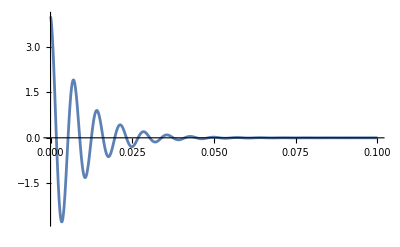

```mathematica
Plot[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1/1000, J-> 280},{t,0,0.1},PlotRange->All]
```

```mathematica
signal2= Total[U2 . {1,1,1,1}];
```

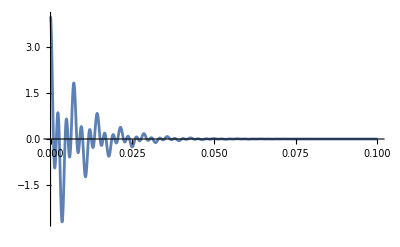

```mathematica
Plot[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1, J-> 280}]],{t,0,0.1},PlotRange->All]
```

### k_0=1

```mathematica
spec1=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (43536 π+715600 π^2+9 (4+ω^2)))/(858720000 π^3+512083360000 π^4+10800 π ω^2+81 ω^2 (4+ω^2)-7200 π^2 (-50+1739 ω^2))

```mathematica
spec2=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((1.74011×10^128+5.00221×10^113 ⅈ)+(1.07552×10^122-7.3392×10^107 ⅈ) ω^2-(2.8438×10^115-1.39984×10^101 ⅈ) ω^4+(7.56788×10^108-8.3437×10^93 ⅈ) ω^6)/((2.7173×10^131+0. ⅈ)-(7.4691×10^125+4.10995×10^108 ⅈ) ω^2+(6.3639×10^119+2.23974×10^102 ⅈ) ω^4-(1.39362×10^113-1.06799×10^96 ⅈ) ω^6+9.0335×10^105 ω^8)

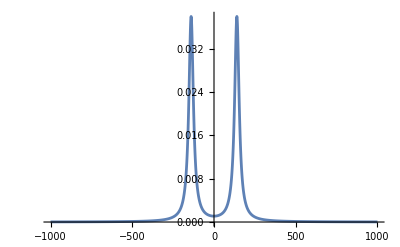

```mathematica
Plot[spec1/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

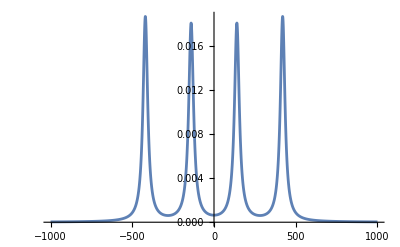

```mathematica
Plot[spec2/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

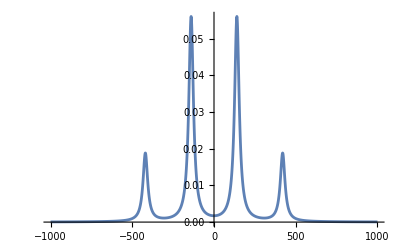

```mathematica
Plot[(spec1+spec2)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

k_0=50

```mathematica
spec1h=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 50, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (90000+2176800 π+715600 π^2+9 ω^2))/(42936000000 π^3+512083360000 π^4+540000 π ω^2+81 ω^2 (10000+ω^2)-7200 π^2 (-125000+1739 ω^2))

```mathematica
spec2h=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/50,Subscript[k, 0]-> 100, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((6.84193×10^124+2.5834×10^109 ⅈ)+(1.29388×10^118+3.30362×10^103 ⅈ) ω^2+(1.45256×10^111+4.27197×10^96 ⅈ) ω^4+(1.12021×10^104+5.09259×10^89 ⅈ) ω^6)/((2.0433×10^127+1.20245×10^112 ⅈ)-(8.63283×10^120-3.58359×10^105 ⅈ) ω^2+(1.37056×10^115+8.54395×10^97 ⅈ) ω^4-(3.58762×10^108-3.91111×10^92 ⅈ) ω^6+2.67431×10^101 ω^8)

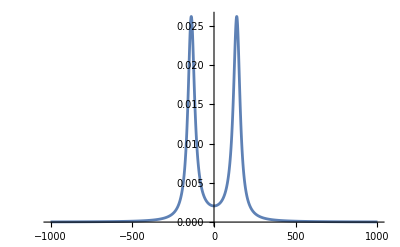

```mathematica
Plot[spec1h/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

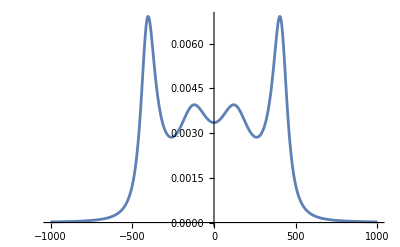

```mathematica
Plot[spec2h/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

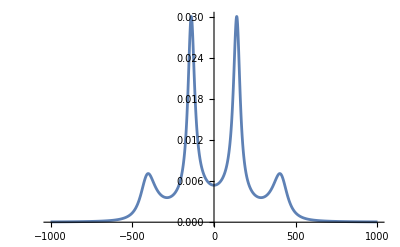

```mathematica
Plot[(spec1h+spec2h)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=100

```mathematica
spec1a=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 100, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (4353600 π+715600 π^2+9 (40000+ω^2)))/(85872000000 π^3+512083360000 π^4+1080000 π ω^2+81 ω^2 (40000+ω^2)-7200 π^2 (-500000+1739 ω^2))

```mathematica
spec2a=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 100, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((4.34662×10^127-1.20245×10^112 ⅈ)+(8.506×10^120-1.3761×10^106 ⅈ) ω^2+(7.18378×10^113+7.65538×10^99 ⅈ) ω^4+(1.23604×10^107-5.54074×10^92 ⅈ) ω^6)/((1.29204×10^130-6.38743×10^114 ⅈ)-(4.03485×10^123+4.69709×10^108 ⅈ) ω^2+(7.34879×10^117+1.67981×10^102 ⅈ) ω^4-(1.94354×10^111+1.00124×10^95 ⅈ) ω^6+1.47542×10^104 ω^8)

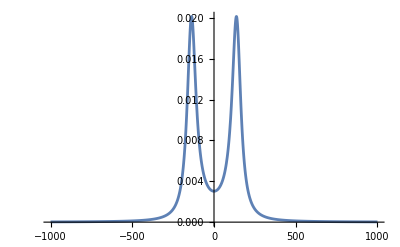

```mathematica
Plot[spec1a/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

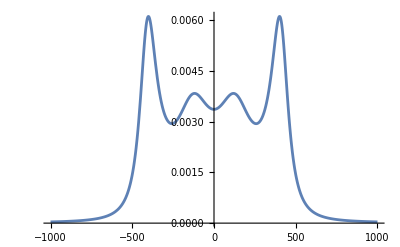

```mathematica
Plot[spec2a/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

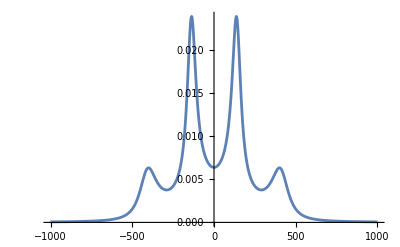

```mathematica
Plot[(spec1a+spec2a)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=200

```mathematica
spec1b=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 200, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (8707200 π+715600 π^2+9 (160000+ω^2)))/(171744000000 π^3+512083360000 π^4+2160000 π ω^2+81 ω^2 (160000+ω^2)-7200 π^2 (-2000000+1739 ω^2))

```mathematica
spec2b=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 200, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((1.2953×10^24+3.0199×10^8 ⅈ)+(1.87997×10^17+16. ⅈ) ω^2+(1.60345×10^10-0.0000572205 ⅈ) ω^4+(837.758+8.18545×10^-12 ⅈ) ω^6)/((3.58259×10^26-3.43597×10^10 ⅈ)+(8.11256×10^19+0. ⅈ) ω^2+(2.64681×10^12+0. ⅈ) ω^4-(7.23392×10^6+0. ⅈ) ω^6+1. ω^8)

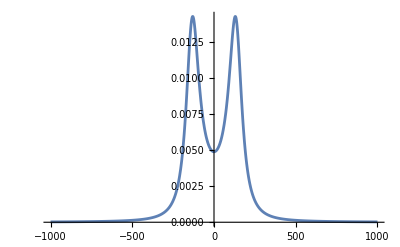

```mathematica
Plot[spec1b/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

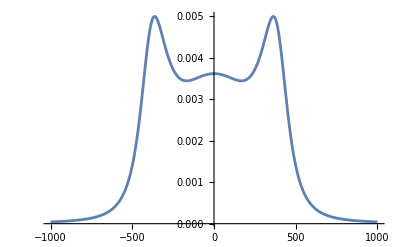

```mathematica
Plot[spec2b/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

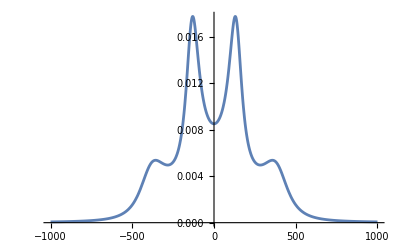

```mathematica
Plot[(spec1b+spec2b)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=300

```mathematica
spec1c=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 300, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (13060800 π+715600 π^2+9 (360000+ω^2)))/(257616000000 π^3+512083360000 π^4+3240000 π ω^2+81 ω^2 (360000+ω^2)-7200 π^2 (-4500000+1739 ω^2))

```mathematica
spec2c=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 300, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((5.96612×10^74+6.84659×10^58 ⅈ)+(7.0355×10^67-1.88779×10^52 ⅈ) ω^2+(4.35588×10^60-2.14584×10^45 ⅈ) ω^4+(1.20502×10^53+7.72498×10^38 ⅈ) ω^6)/((1.68962×10^77+0. ⅈ)+(2.06037×10^70+0. ⅈ) ω^2-(6.84345×10^63+0. ⅈ) ω^4+(3.43051×10^56+0. ⅈ) ω^6+1.43839×10^50 ω^8)

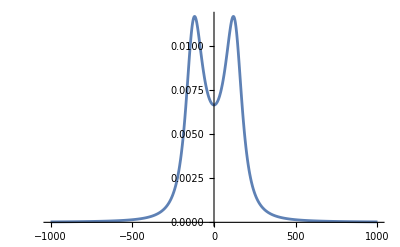

```mathematica
Plot[spec1c/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

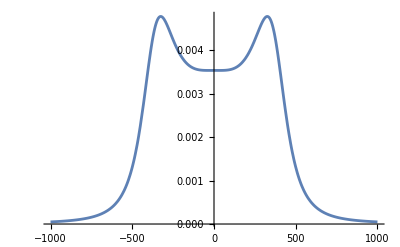

```mathematica
Plot[spec2c/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

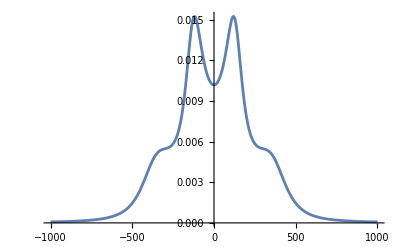

```mathematica
Plot[(spec1c+spec2c)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=400

```mathematica
spec1d=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 400, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (17414400 π+715600 π^2+9 (640000+ω^2)))/(343488000000 π^3+512083360000 π^4+4320000 π ω^2+81 ω^2 (640000+ω^2)-7200 π^2 (-8000000+1739 ω^2))

```mathematica
spec2d=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 400, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((4.07945×10^76+1.0031×10^61 ⅈ)+(3.97085×10^69+2.60223×10^53 ⅈ) ω^2+(1.78472×10^62-6.60154×10^46 ⅈ) ω^4+(3.14014×10^54+1.15987×10^40 ⅈ) ω^6)/((1.15395×10^79+0. ⅈ)+(9.96303×10^70+0. ⅈ) ω^2-(2.37146×10^65+0. ⅈ) ω^4+(5.87872×10^58+0. ⅈ) ω^6+3.74827×10^51 ω^8)

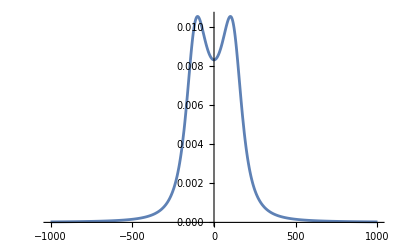

```mathematica
Plot[spec1d/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

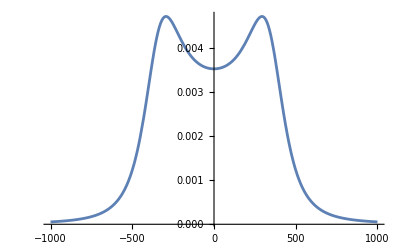

```mathematica
Plot[spec2d/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

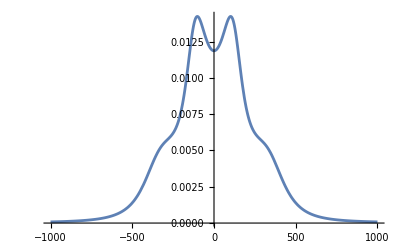

```mathematica
Plot[(spec1d+spec2d)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

## k_0=450

(2400 π (19591200 π+715600 π^2+9 (810000+ω^2)))/(386424000000 π^3+512083360000 π^4+4860000 π ω^2+81 ω^2 (810000+ω^2)-7200 π^2 (-10125000+1739 ω^2))

((2.84733×10^82-2.62574×10^66 ⅈ)+(2.5235×10^75+1.16395×10^59 ⅈ) ω^2+(9.79714×10^67-2.7685×10^53 ⅈ) ω^4+(1.429×10^60-6.84494×10^45 ⅈ) ω^6)/((7.9616×10^84+0. ⅈ)-(2.37716×10^77+0. ⅈ) ω^2-(7.25635×10^70+0. ⅈ) ω^4+(4.04487×10^64+0. ⅈ) ω^6+1.70574×10^57 ω^8)

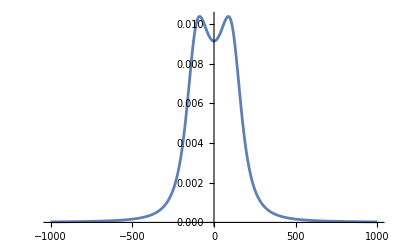

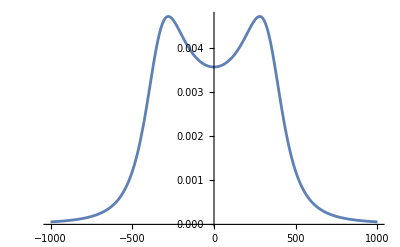

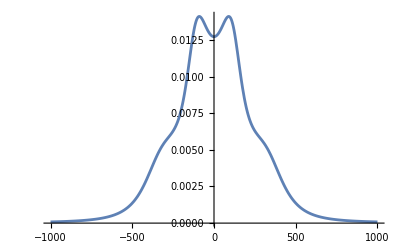

```mathematica
spec1x=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 450, J-> 280},t,ω,FourierParameters->{1,-1}]
spec2x=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 450, J-> 280}]],t,ω,FourierParameters->{1,-1}]
Plot[spec1x/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
Plot[spec2x/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
Plot[(spec1x+spec2x)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

k_0=500

```mathematica
spec1f=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 500, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (9000000+21768000 π+715600 π^2+9 ω^2))/(429360000000 π^3+512083360000 π^4+5400000 π ω^2+81 ω^2 (1000000+ω^2)-7200 π^2 (-12500000+1739 ω^2))

```mathematica
spec2f=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 500, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((1.81569×10^75+1.29194×10^58 ⅈ)+(1.46745×10^68+1.35349×10^52 ⅈ) ω^2+(4.96911×10^60+1.59931×10^45 ⅈ) ω^4+(6.11933×10^52-5.61735×10^38 ⅈ) ω^6)/((4.99014×10^77+0. ⅈ)-(2.87115×10^70+0. ⅈ) ω^2+(5.36054×10^62+0. ⅈ) ω^4+(2.38582×10^57+0. ⅈ) ω^6+7.30442×10^49 ω^8)

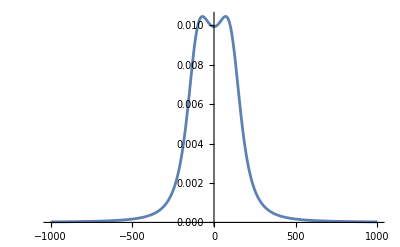

```mathematica
Plot[spec1f/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

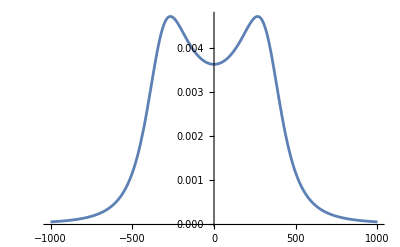

```mathematica
Plot[spec2f/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

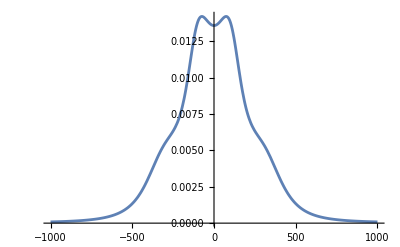

```mathematica
Plot[(spec1f+spec2f)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

k_0=750

```mathematica
spec1g=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 750, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (32652000 π+715600 π^2+9 (2250000+ω^2)))/(644040000000 π^3+512083360000 π^4+8100000 π ω^2+81 ω^2 (2250000+ω^2)-7200 π^2 (-28125000+1739 ω^2))

```mathematica
spec2g=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 750, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((1.63135×10^77-3.69828×10^61 ⅈ)+(8.5905×10^69-8.25874×10^54 ⅈ) ω^2+(1.65673×10^62+8.5548×10^46 ⅈ) ω^4+(1.04709×10^54+5.55921×10^39 ⅈ) ω^6)/((3.92591×10^79+0. ⅈ)-(3.50749×10^72+0. ⅈ) ω^2+(1.28608×10^66+0. ⅈ) ω^4+(1.14×10^59+0. ⅈ) ω^6+1.24987×10^51 ω^8)

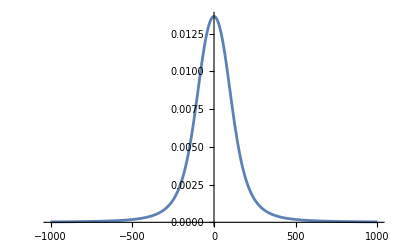

```mathematica
Plot[spec1g/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

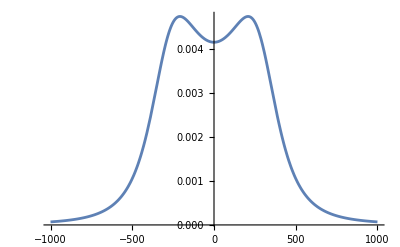

```mathematica
Plot[spec2g/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

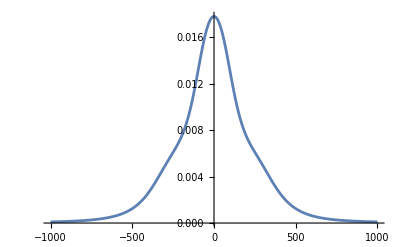

```mathematica
Plot[(spec1g+spec2g)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

### k_0=1000

```mathematica
spec1e=FourierTransform[signal1//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1000, J-> 280},t,ω,FourierParameters->{1,-1}]
```

(2400 π (43536000 π+715600 π^2+9 (4000000+ω^2)))/(858720000000 π^3+512083360000 π^4+10800000 π ω^2+81 ω^2 (4000000+ω^2)-7200 π^2 (-50000000+1739 ω^2))

```mathematica
spec2e=FourierTransform[Simplify[N[signal2//. {Subscript[T, 2]-> 3/100,Subscript[k, 0]-> 1000, J-> 280}]],t,ω,FourierParameters->{1,-1}]
```

((3.13985×10^77+4.62706×10^61 ⅈ)+(1.14759×10^70-1.70022×10^55 ⅈ) ω^2+(1.44885×10^62-8.73791×10^47 ⅈ) ω^4+(5.61043×10^53-6.36925×10^39 ⅈ) ω^6)/((6.47803×10^79+0. ⅈ)-(1.65989×10^72+0. ⅈ) ω^2+(2.98583×10^66+0. ⅈ) ω^4+(1.15695×10^59+0. ⅈ) ω^6+6.69695×10^50 ω^8)

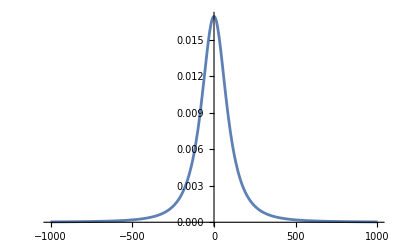

```mathematica
Plot[spec1e/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

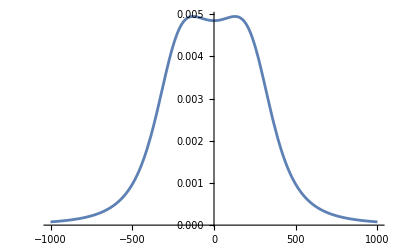

```mathematica
Plot[spec2e/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

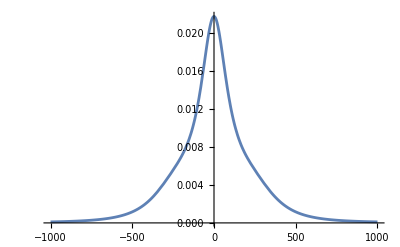

```mathematica
Plot[(spec1e+spec2e)/. ω-> z*(2π),{z,-1000,1000},PlotRange->All]
```

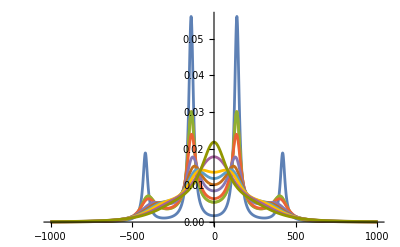

```mathematica
Plot[{(spec1+spec2)/. ω-> z*(2π),(spec1h+spec2h)/. ω-> z*(2π),(spec1h+spec2h)/. ω-> z*(2π),(spec1a+spec2a)/. ω-> z*(2π),(spec1b+spec2b)/. ω-> z*(2π),(spec1c+spec2c)/. ω-> z*(2π),(spec1d+spec2d)/. ω-> z*(2π),(spec1f+spec2f)/. ω-> z*(2π),(spec1g+spec2g)/. ω-> z*(2π), (spec1e+spec2e)/. ω-> z*(2π)},{z,-1000,1000},PlotRange->All]
```